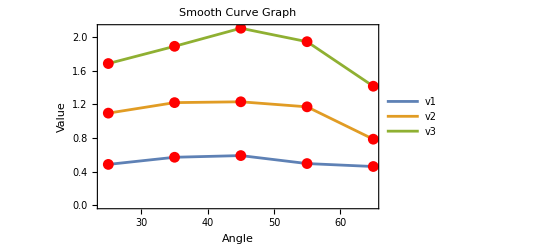

```mathematica
data={{25,0.485},{35,0.570},{45,0.590},{55,0.495},{65,0.460}};
newData={{25,1.095},{35,1.220},{45,1.230},{55,1.170},{65,0.785}};
latestData={{25,1.685},{35,1.890},{45,2.105},{55,1.945},{65,1.415}};

v1=data[[All,2]];
v2=newData[[All,2]];
v3=latestData[[All,2]];

ListLinePlot[{v1,v2,v3},DataRange->{25,65},PlotLegends->{"v1","v2","v3"},Mesh->All,MeshStyle->Red,Frame->True,FrameLabel->{"Angle","Value"},PlotLabel->"Smooth Curve Graph"]
```

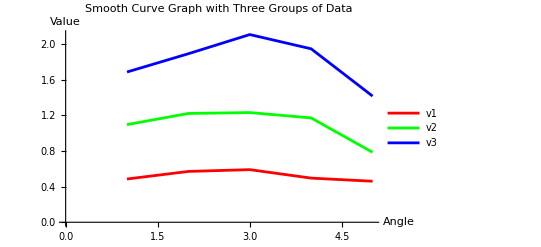

```mathematica
data={{25,0.485},{35,0.570},{45,0.590},{55,0.495},{65,0.460}};
newData={{25,1.095},{35,1.220},{45,1.230},{55,1.170},{65,0.785}};
latestData={{25,1.685},{35,1.890},{45,2.105},{55,1.945},{65,1.415}};

(*Extracting the second element (v1,v2,v3) from each list*)
v1=data[[All,2]];
v2=newData[[All,2]];
v3=latestData[[All,2]];

(*Plotting the smooth curve graph*)
ListLinePlot[{v1,v2,v3},PlotStyle->{Red,Green,Blue},PlotLegends->{"v1","v2","v3"},AxesLabel->{"Angle","Value"},PlotLabel->"Smooth Curve Graph with Three Groups of Data"]
```

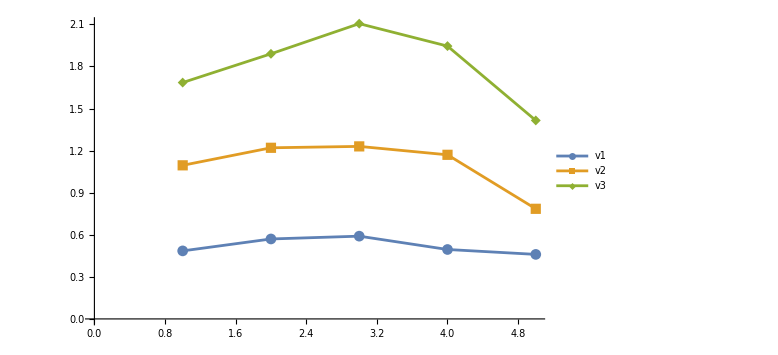

```mathematica
data={{25,0.485},{35,0.570},{45,0.590},{55,0.495},{65,0.460}};
newData={{25,1.095},{35,1.220},{45,1.230},{55,1.170},{65,0.785}};
latestData={{25,1.685},{35,1.890},{45,2.105},{55,1.945},{65,1.415}};

(*Extracting the second element (v1,v2,v3) from each list*)
v1=data[[All,2]];
v2=newData[[All,2]];
v3=latestData[[All,2]];

(*Creating a smooth curve line plot*)
ListLinePlot[{v1,v2,v3},PlotLegends->{"v1","v2","v3"},Mesh->All,MeshStyle->PointSize[Medium],ImageSize->Large,PlotMarkers->Automatic]
```

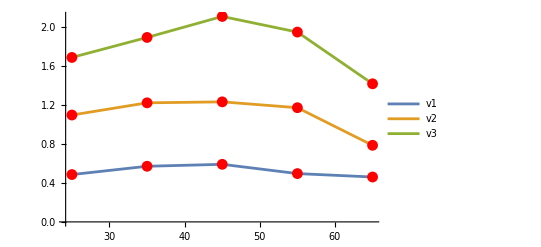

```mathematica
data={{25,0.485},{35,0.570},{45,0.590},{55,0.495},{65,0.460}};
newData={{25,1.095},{35,1.220},{45,1.230},{55,1.170},{65,0.785}};
latestData={{25,1.685},{35,1.890},{45,2.105},{55,1.945},{65,1.415}};

v1=data[[All,2]];
v2=newData[[All,2]];
v3=latestData[[All,2]];

ListLinePlot[{v1,v2,v3},DataRange->{25,65},PlotLegends->{"v1","v2","v3"},Mesh->All,MeshStyle->Red]
```

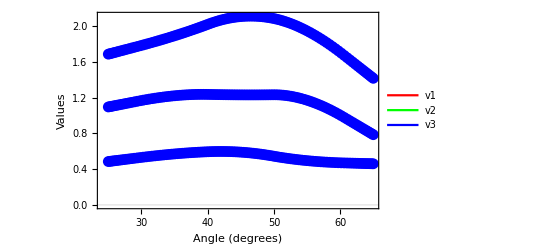

```mathematica
data={{25,0.485},{35,0.570},{45,0.590},{55,0.495},{65,0.460}};
newData={{25,1.095},{35,1.220},{45,1.230},{55,1.170},{65,0.785}};
latestData={{25,1.685},{35,1.890},{45,2.105},{55,1.945},{65,1.415}};

v1=data[[All,2]];
v2=newData[[All,2]];
v3=latestData[[All,2]];

ListLinePlot[{v1,v2,v3},DataRange->{25,65},PlotLegends->{"v1","v2","v3"},AxesLabel->{"Angle (degrees)","Values"},PlotStyle->{Red,Green,Blue},MeshStyle->{Red,Green,Blue},MeshFunctions->{#1&},Mesh->All,InterpolationOrder->2,PlotTheme->"Scientific"]
```

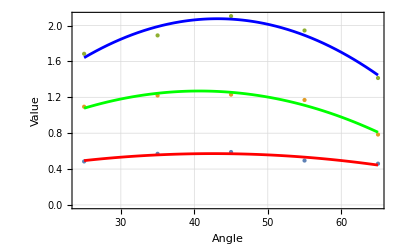

```mathematica
data={{25,0.485},{35,0.570},{45,0.590},{55,0.495},{65,0.460}};
newData={{25,1.095},{35,1.220},{45,1.230},{55,1.170},{65,0.785}};
latestData={{25,1.685},{35,1.890},{45,2.105},{55,1.945},{65,1.415}};

(*Extracting x and y values for each group*)
x1=data[[All,1]];
y1=data[[All,2]];
x2=newData[[All,1]];
y2=newData[[All,2]];
x3=latestData[[All,1]];
y3=latestData[[All,2]];

(*Fitting curves for each group*)
fit1=Fit[Transpose[{x1,y1}],{1,x,x^2},x];
fit2=Fit[Transpose[{x2,y2}],{1,x,x^2},x];
fit3=Fit[Transpose[{x3,y3}],{1,x,x^2},x];

(*Plotting the data points and best-fit curves*)
Show[ListPlot[{data,newData,latestData},PlotStyle->PointSize[Medium]],Plot[{fit1,fit2,fit3},{x,Min[x1],Max[x3]},PlotStyle->{Red,Green,Blue}],Frame->True,FrameLabel->{"Angle","Value"},GridLines->Automatic,PlotLegends->{"v1","v2","v3"}]
```

```mathematica
data={{25,0.485},{35,0.570},{45,0.590},{55,0.495},{65,0.460}};
newData={{25,1.095},{35,1.220},{45,1.230},{55,1.170},{65,0.785}};
latestData={{25,1.685},{35,1.890},{45,2.105},{55,1.945},{65,1.415}};

v1=data[[All,2]];
v2=newData[[All,2]];
v3=latestData[[All,2]];

(*Forming a graph with best-fit curve for each group*)
ListPlot[{Transpose[{data[[All,1]],v1}],Transpose[{newData[[All,1]],v2}],Transpose[{latestData[[All,1]],v3}]},PlotStyle->{Red,Green,Blue},PlotLegends->{"v1","v2","v3"},AxesLabel->{"Angle","Value"},PlotLabel->"Data with Best-Fit Curve"]
```

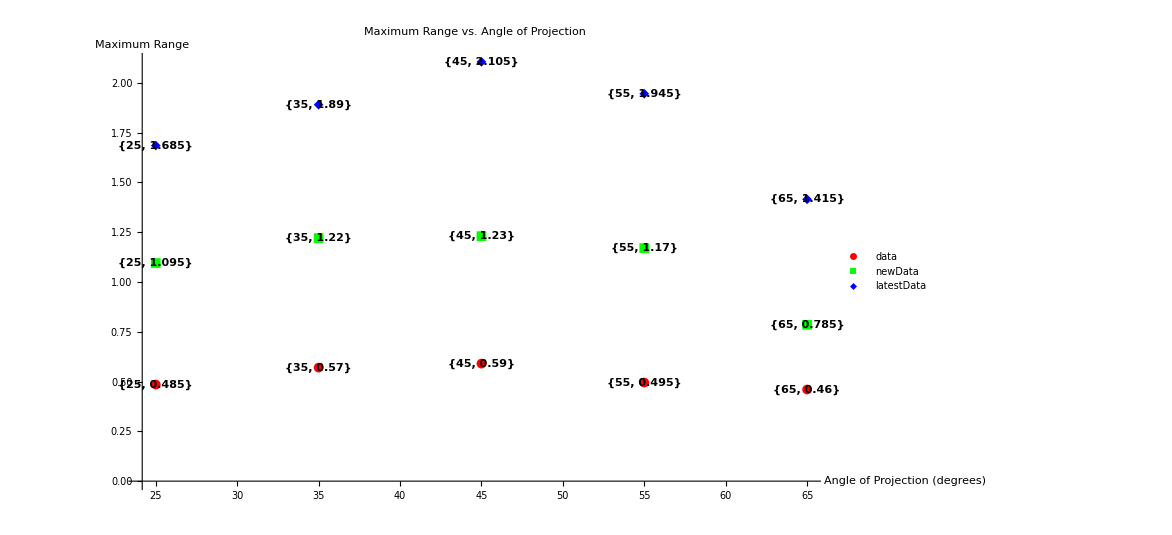

```mathematica
data={{25,0.485},{35,0.570},{45,0.590},{55,0.495},{65,0.460}};
newData={{25,1.095},{35,1.220},{45,1.230},{55,1.170},{65,0.785}};
latestData={{25,1.685},{35,1.890},{45,2.105},{55,1.945},{65,1.415}};

angles={25,35,45,55,65};

ListPlot[Transpose[{angles,#}]&/@{v1,v2,v3},PlotStyle->{Red,Green,Blue},PlotMarkers->{Automatic,Medium},PlotLegends->{"data","newData","latestData"},Epilog->{Text[Style[ToString[#],Black,Bold],#,{1,0}]&/@data,Text[Style[ToString[#],Black,Bold],#,{1,0}]&/@newData,Text[Style[ToString[#],Black,Bold],#,{1,0}]&/@latestData},AxesLabel->{"Angle of Projection (degrees)","Maximum Range"},PlotLabel->"Maximum Range vs. Angle of Projection",ImageSize->Medium]
```

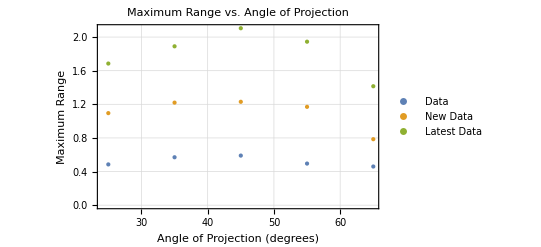

```mathematica
data={{25,0.485},{35,0.570},{45,0.590},{55,0.495},{65,0.460}};
newData={{25,1.095},{35,1.220},{45,1.230},{55,1.170},{65,0.785}};
latestData={{25,1.685},{35,1.890},{45,2.105},{55,1.945},{65,1.415}};

angles=data[[All,1]];  (*Assuming the first element of each sublist is the angle in degrees*)
ranges1=data[[All,2]];
ranges2=newData[[All,2]];
ranges3=latestData[[All,2]];

ListPlot[{Transpose[{angles,ranges1}],Transpose[{angles,ranges2}],Transpose[{angles,ranges3}]},PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium]},PlotLegends->{"Data","New Data","Latest Data"},Frame->True,GridLines->Automatic,FrameLabel->{"Angle of Projection (degrees)","Maximum Range"},PlotLabel->"Maximum Range vs. Angle of Projection"]
```